```mathematica
ClearAll["Global`*"];
```

```mathematica
(*НЕОБХОДИМЫЕ ПЕРЕМЕННЫЕ И ФУНКЦИИ*)
ϵ=10^(-3);znak=3; 
X0={-1,-2};α=1;f[{x_,y_}]:=α(x^2-y)^2+(x-1)^2
(*X0={√10,0};f[{x_,y_}]:=11 x^2+3 y^2+6x y-2 √10(x-3y)-22;*)(*X0={√10,0};X0={0,√10};*)
antiGradF[{x1_,x2_}]:=-Grad[f[{x,y}],{x,y}]/.{x->x1,y->x2}
NormGradF[{x_,y_}]:=Norm[antiGradF[{x,y}]]
uniformMesh[left_,right_,n_]:=Table[i,{i,left,right,(right-left)/n}]
X=X0;
P=antiGradF[X0];
points={X0};
norm={NormGradF[X0]};
ωArray={P};
fValues={f[X0]};

A={{1,0},{0,1}};
ΔA={{1,0},{0,1}};
ΔX={0,0};Δ𝒳={0,0};
Δω={0,0};R={0,0};

symi=0;i=0;
ifunk={0};

(*АЛГОРИТМ*)
restart:=False;re=0;
While[norm[[-1]]≥ϵ,
i=0;
κ=NArgMin[f[X+y P],y,StepMonitor:>i++];
X+=κ P;re++;  
points=Append[points,X];
fValues=Append[fValues,f[X]];i++;
ωArray=Append[ωArray,antiGradF[X]];i+=3;
norm=Append[norm,Norm[ωArray[[-1]]]];  
ΔX=κ P;
Δω=ωArray[[-1]]-ωArray[[-2]];
If[(restart) && (Mod[re,2]==0) ,A={{1,0},{0,1}},  
(*Метод Давидона-Флетчера-Пауэлла (ДФП)*)
ΔA=-KroneckerProduct[ΔX,ΔX]/(Δω.ΔX)-KroneckerProduct[A.Δω,A.Δω]/((A.Δω).Δω);
(*Метод Бройдена-Пауэлла-Гольдфарба-Шенно(ДПГШ)*)
(*R=(A.Δω)/((A.Δω).Δω)-ΔX/(Δω.ΔX);   ΔA=-KroneckerProduct[ΔX,ΔX]/(Δω.ΔX)-KroneckerProduct[A.Δω,A.Δω]/((A.Δω).Δω)+((A.Δω).Δω) KroneckerProduct[R,R];*)
(*Δ𝒳=ΔX+A.Δω;ΔA=-KroneckerProduct[Δ𝒳,Δ𝒳]/(Δω.Δ𝒳);*)(*Пауэлла*)
(*ΔA=-KroneckerProduct[ΔX+A.Δω,ΔX]/(Δω.ΔX);*)(*Мак-Кормика*)
A+=ΔA; ];

   P=A.  ωArray[[-1]];   
symi+=i;        ifunk=Append[ifunk,i]; ];"Результат получен за "<>ToString[Length[points]-1]<> " итер. Точка минимума X = "<>ToString[SetAccuracy[X,znak]]<>". Функция f(x) в алгоритме была вычислена "<>ToString[symi]<>" раз."
SetAccuracy[f[X],znak]" - минимум функции f(X)"
```

Результат получен за 7 итер. Точка минимума X = {1.0, 1.0}. Функция f(x) в алгоритме была вычислена 476 раз.

0.  - минимум функции f(X)

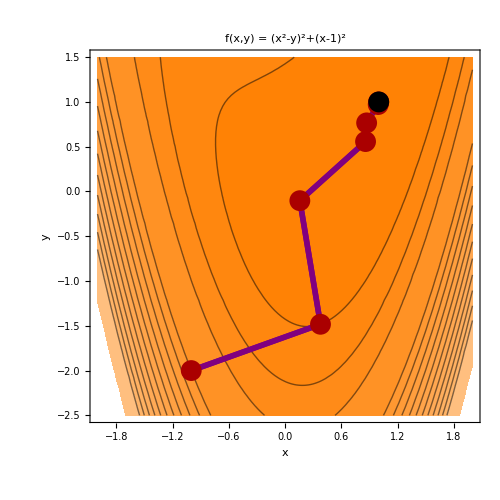

```mathematica
(*ГРАФИК ПОИСКА ТОЧКИ МИНИМУМА*)
a:=Length[points]-1;b:=Length[points];
c:=5; CP0={-2,-2.5}; CP1={2,1.5};
(*c:=5; CP0={-2,-2.5}; CP1={2,1.5};(*Функция Розенброка при лямбда = 1,50,1000*)*)

(*CP0={-3,-2.5}; CP1={3,3.5};c:=20;(*(ДФП) Функция Розенброка при лямбда = 1000 c Рестартами*)*)

(*CP0={-9.5,-3}; CP1={12,19.5};c:=20;(*(ДПГШ) Функция Розенброка при лямбда = 1000 без Рестартов*)*)
(*CP0={-12.5,-3}; CP1={12,21.5};c:=20;(*(ДПГШ) Функция Розенброка при лямбда = 1000 c Рестартами*)*)

(*CP0={-4,-3}; CP1={4,5};c:=20;(*(Пауэлл) Функция Розенброка при лямбда = 1000 c Рестартами*)*)

(*c:=b; CP0={-1,-5}; CP1={5,1}; Квадратичная функция с нач приближ X0={√10,0};*)
(*c:=b; CP0={-4.5,-5}; CP1={4,3.5}; Квадратичная функция с нач приближ X0={0,√10};*)

ContourPlot[f[{x,y}],{x,CP0[[1]],CP1[[1]]},{y,CP0[[2]],CP1[[2]]},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;2]]~Join~{fValues[[a]],fValues[[b]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large](*,LabelStyle->Large*),FrameStyle->Thick,ImageSize->500,Epilog->{Purple,Thickness[0.008],Line[points],Table[Arrow[points[[i-1;;i]]],{i,2,c}],Darker[Red],PointSize[0.03],Point[points],Black,Point[points[[Length[points]]]]}]
```

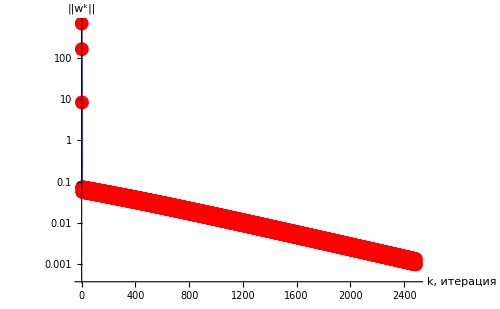

```mathematica
ListLogPlot[norm,DataRange->{0,Length[points]-1},PlotRange->All,PlotStyle->{Blue,Thick,PointSize[Large]},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||w^k||"},ImageSize->500,Joined->True,Mesh->Full,MeshStyle->Directive[PointSize[0.02],Red]]
```

```mathematica
gridLabel={"k","X^k","f(X^k)","||w^k||"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,Length[points]}];gridData[[All,1]]=Table[i,{i,0,Length[points]-1}];
For[i=1,i≤Length[points],i++,gridData[[i,2]]="("<>ToString[SetAccuracy[points[[i,1]],znak]]<>", "<>ToString[SetAccuracy[points[[i,2]],znak]]<>")"]
gridData[[All,3]]=SetAccuracy[fValues,znak];
gridData[[All,4]]=SetAccuracy[norm,znak];
gridData={gridLabel}~Join~gridData;Grid[gridData,Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]]
```

k | X^k | f(X^k) | ||w^k||
0 | (     -3
0. 10, 3.162) | 68. | 40.
1 | (-1.13, -0.23) | -3.43 | 34.29
2 | (1.58, -4.74) | -72. | 0.